```mathematica
names={"prog1.txt","prog2.txt","prog3.txt"};
imp=Table[Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>names[[i]],"Table"],{i,1,Length[names]}];
data=imp
```

{{{510.38,20648.4},{511.39,21416.2},{512.31,22169.8},{513.12,22594.8},{514.23,24139.3},{515.55,24918.6},{516.75,25676.8},{518.06,26152.2},{519.36,27342.},{520.86,28514.8},{522.45,28514.1},{524.03,30137.6},{525.52,31489.5},{527.29,32406.1},{528.95,33866.4},{530.91,36006.5},{532.95,36370.8},{534.88,37365.},{536.81,38085.2},{539.11,37937.6},{541.3,37900.8},{543.48,38449.9},{545.74,39060.8},{548.18,40202.9},{550.78,41168.5},{553.37,43897.2},{556.22,43105.3},{558.86,43389.9},{561.84,44442.5},{564.62,44223.9}},{{545.27,40795.2},{547.43,42538.1},{549.95,43011.8},{552.36,43579.},{554.75,43685.8},{557.31,43573.6},{559.86,44733.5},{562.74,43093.5},{565.51,42056.3},{568.53,41244.5},{571.61,40516.4},{574.74,39839.5},{578.1,38753.1},{581.6,38001.},{584.97,37887.3},{588.39,36955.},{592.1,37770.3},{595.84,37995.2},{599.77,39063.6},{603.56,39868.5},{607.45,40721.4},{611.58,41522.3}},{{569.41,44092.},{572.13,42262.5},{575.35,40850.6},{578.45,39297.2},{581.77,38222.6},{585.23,38104.4},{588.64,37136.5},{592.1,37770.3},{595.84,37995.2},{599.61,38881.9},{603.4,39959.7},{607.45,40721.4},{611.43,41704.9}}}

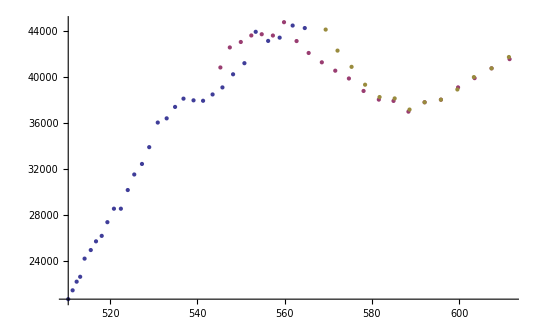

```mathematica
ListPlot[data]
```

```mathematica
ν0=Table[{48-i,data[[1,i,1]]},{i,1,Length[data[[1]]]}]
ν1=Table[{29-i,data[[2,i,1]]},{i,1,Length[data[[2]]]}]
ν2=Table[{22-i,data[[3,i,1]]},{i,1,Length[data[[3]]]}]
ν0[[All,2]]=10^7/ν0[[All,2]];
ν1[[All,2]]=10^7/ν1[[All,2]];
ν2[[All,2]]=10^7/ν2[[All,2]];
ν0
ν1
ν2
```

{{47,510.38},{46,511.39},{45,512.31},{44,513.12},{43,514.23},{42,515.55},{41,516.75},{40,518.06},{39,519.36},{38,520.86},{37,522.45},{36,524.03},{35,525.52},{34,527.29},{33,528.95},{32,530.91},{31,532.95},{30,534.88},{29,536.81},{28,539.11},{27,541.3},{26,543.48},{25,545.74},{24,548.18},{23,550.78},{22,553.37},{21,556.22},{20,558.86},{19,561.84},{18,564.62}}

{{28,545.27},{27,547.43},{26,549.95},{25,552.36},{24,554.75},{23,557.31},{22,559.86},{21,562.74},{20,565.51},{19,568.53},{18,571.61},{17,574.74},{16,578.1},{15,581.6},{14,584.97},{13,588.39},{12,592.1},{11,595.84},{10,599.77},{9,603.56},{8,607.45},{7,611.58}}

{{21,569.41},{20,572.13},{19,575.35},{18,578.45},{17,581.77},{16,585.23},{15,588.64},{14,592.1},{13,595.84},{12,599.61},{11,603.4},{10,607.45},{9,611.43}}

{{47,19593.2},{46,19554.5},{45,19519.4},{44,19488.6},{43,19446.6},{42,19396.8},{41,19351.7},{40,19302.8},{39,19254.5},{38,19199.},{37,19140.6},{36,19082.9},{35,19028.8},{34,18964.9},{33,18905.4},{32,18835.6},{31,18763.5},{30,18695.8},{29,18628.6},{28,18549.1},{27,18474.},{26,18399.9},{25,18323.7},{24,18242.2},{23,18156.1},{22,18071.1},{21,17978.5},{20,17893.6},{19,17798.7},{18,17711.}}

{{28,18339.5},{27,18267.2},{26,18183.5},{25,18104.1},{24,18026.1},{23,17943.3},{22,17861.6},{21,17770.2},{20,17683.2},{19,17589.2},{18,17494.4},{17,17399.2},{16,17298.},{15,17193.9},{14,17094.9},{13,16995.5},{12,16889.},{11,16783.},{10,16673.1},{9,16568.4},{8,16462.3},{7,16351.1}}

{{21,17562.},{20,17478.5},{19,17380.7},{18,17287.6},{17,17188.9},{16,17087.3},{15,16988.3},{14,16889.},{13,16783.},{12,16677.5},{11,16572.8},{10,16462.3},{9,16355.1}}

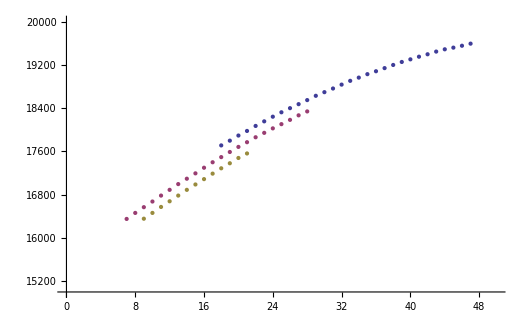

```mathematica
ListPlot[{Tooltip[ν0],Tooltip[ν1],Tooltip[ν2]},PlotRange->{{0,50},{15000,20000}}]
```

```mathematica
Δν0=Table[{ν0[[i,1]]+0.5,ν0[[i,2]]-ν0[[i+1,2]]},{i,1,Length[ν0]-1}]
Δν1=Table[{ν1[[i,1]]+0.5,ν1[[i,2]]-ν1[[i+1,2]]},{i,1,Length[ν1]-1}]
Δν2=Table[{ν2[[i,1]]+0.5,ν2[[i,2]]-ν2[[i+1,2]]},{i,1,Length[ν2]-1}]
```

{{47.5,38.6968},{46.5,35.1158},{45.5,30.8129},{44.5,42.0675},{43.5,49.7904},{42.5,45.0433},{41.5,48.934},{40.5,48.3164},{39.5,55.45},{38.5,58.4294},{37.5,57.7107},{36.5,54.1054},{35.5,63.8755},{34.5,59.5174},{33.5,69.7944},{32.5,72.0979},{31.5,67.704},{30.5,67.2172},{29.5,79.4749},{28.5,75.0462},{27.5,74.1028},{26.5,76.1972},{25.5,81.5607},{24.5,86.1137},{23.5,84.9779},{22.5,92.594},{21.5,84.9287},{20.5,94.9075},{19.5,87.6347}}

{{28.5,72.3625},{27.5,83.7045},{26.5,79.3362},{25.5,77.9971},{24.5,82.803},{23.5,81.7267},{22.5,91.4124},{21.5,87.0426},{20.5,93.9319},{19.5,94.7758},{18.5,95.2737},{17.5,101.126},{16.5,104.098},{15.5,99.054},{14.5,99.3636},{13.5,106.491},{12.5,106.01},{11.5,109.971},{10.5,104.697},{9.5,106.101},{8.5,111.17}}

{{21.5,83.4928},{20.5,97.8203},{19.5,93.1459},{18.5,98.6554},{17.5,101.624},{16.5,98.987},{15.5,99.273},{14.5,106.01},{13.5,105.522},{12.5,104.753},{11.5,110.494},{10.5,107.158}}

FittedModel[120.629-0.555977 (2+2 x)-0.00459212 (13/4+6 x+3 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 120.629 | 13.6578 | 8.83225 | 2.63302×10^-9
b | 0.555977 | 0.411725 | 1.35036 | 0.188538
c | -0.00459212 | 0.00395491 | -1.16112 | 0.256143

(186.536 | 5.57572 | 0.0525625
5.57572 | 0.169517 | 0.00161887
0.0525625 | 0.00161887 | 0.0000156413)

(1. | 0.991547 | 0.973104
0.991547 | 1. | 0.994191
0.973104 | 0.994191 | 1.)

FittedModel[114.541-0.0439943 (2+2 x)-0.0144986 (13/4+6 x+3 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 114.541 | 7.88243 | 14.5312 | 2.1901×10^-11
b | 0.0439943 | 0.430142 | 0.102278 | 0.919666
c | -0.0144986 | 0.00728343 | -1.99062 | 0.0619271

(62.1327 | 3.3336 | 0.0546664
3.3336 | 0.185022 | 0.00310333
0.0546664 | 0.00310333 | 0.0000530484)

(1. | 0.983198 | 0.952191
0.983198 | 1. | 0.990558
0.952191 | 0.990558 | 1.)

FittedModel[93.147+1.41239 (2+2 x)-0.0449504 (13/4+6 x+3 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 93.147 | 26.9227 | 3.45979 | 0.00716315
b | -1.41239 | 1.6294 | -0.866814 | 0.408559
c | -0.0449504 | 0.0318208 | -1.41261 | 0.191404

(724.833 | 43.6365 | 0.841442
43.6365 | 2.65495 | 0.0516408
0.841442 | 0.0516408 | 0.00101257)

(1. | 0.994725 | 0.982186
0.994725 | 1. | 0.995987
0.982186 | 0.995987 | 1.)

109.439

-0.270806

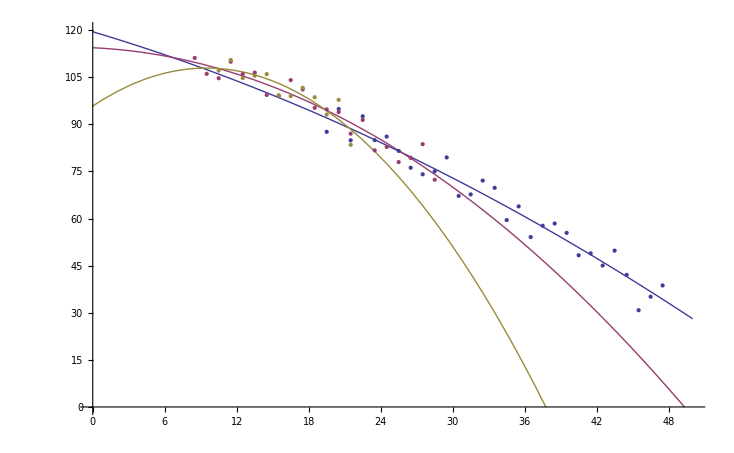

```mathematica
m0=NonlinearModelFit[Δν0,a- b(2x+2)+c (3 x^2+6x+13/4),{a,b,c},x]
m0["ParameterTable"]
m0["CovarianceMatrix"]//MatrixForm
m0["CorrelationMatrix"]//MatrixForm

m1=NonlinearModelFit[Δν1,a- b(2x+2)+c (3 x^2+6x+13/4),{a,b,c},x]
m1["ParameterTable"]
m1["CovarianceMatrix"]//MatrixForm
m1["CorrelationMatrix"]//MatrixForm

m2=NonlinearModelFit[Δν2,a- b(2x+2)+c (3 x^2+6x+13/4),{a,b,c},x]
m2["ParameterTable"]
m2["CovarianceMatrix"]//MatrixForm
m2["CorrelationMatrix"]//MatrixForm

(m0["ParameterTableEntries"][[1,1]]+m1["ParameterTableEntries"][[1,1]]+m2["ParameterTableEntries"][[1,1]])/3
(m0["ParameterTableEntries"][[2,1]]+m1["ParameterTableEntries"][[2,1]]+m2["ParameterTableEntries"][[2,1]])/3

Show[Plot[{Normal[m0],Normal[m1],Normal[m2]},{x,0,50},PlotRange->{{0,50},{0,120}}],ListPlot[{Δν0,Δν1,Δν2}]]
```

FittedModel[136.061-1.03126 (2+2 x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 136.061 | 3.16654 | 42.9683 | 2.13037×10^-26
b | 1.03126 | 0.0445992 | 23.1229 | 2.49823×10^-19

(10.027 | 0.137247
0.137247 | 0.00198909)

(1. | 0.971831
0.971831 | 1.)

FittedModel[129.482-0.89216 (2+2 x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 129.482 | 2.58906 | 50.0113 | 1.23874×10^-21
b | 0.89216 | 0.0633997 | 14.072 | 1.68336×10^-11

(6.70323 | 0.156762
0.156762 | 0.00401953)

(1. | 0.955015
0.955015 | 1.)

FittedModel[130.501-0.880083 (2+2 x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 130.501 | 5.30495 | 24.5998 | 2.81289×10^-10
b | 0.880083 | 0.152907 | 5.75567 | 0.000183739

(28.1425 | 0.794941
0.794941 | 0.0233806)

(1. | 0.979999
0.979999 | 1.)

132.015

0.934501

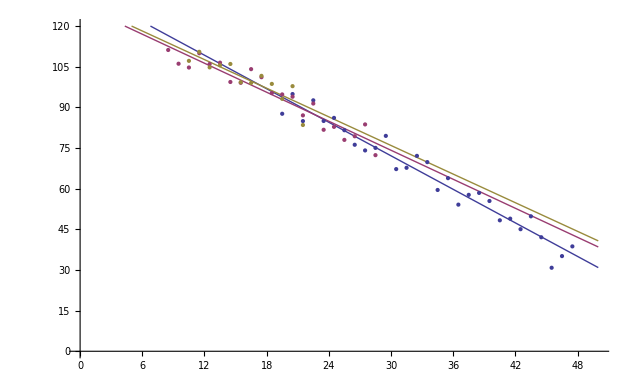

```mathematica
m0=NonlinearModelFit[Δν0,a- b(2x+2),{a,b},x]
m0["ParameterTable"]
m0["CovarianceMatrix"]//MatrixForm
m0["CorrelationMatrix"]//MatrixForm

m1=NonlinearModelFit[Δν1,a- b(2x+2),{a,b},x]
m1["ParameterTable"]
m1["CovarianceMatrix"]//MatrixForm
m1["CorrelationMatrix"]//MatrixForm

m2=NonlinearModelFit[Δν2,a- b(2x+2),{a,b},x]
m2["ParameterTable"]
m2["CovarianceMatrix"]//MatrixForm
m2["CorrelationMatrix"]//MatrixForm

(m0["ParameterTableEntries"][[1,1]]+m1["ParameterTableEntries"][[1,1]]+m2["ParameterTableEntries"][[1,1]])/3
(m0["ParameterTableEntries"][[2,1]]+m1["ParameterTableEntries"][[2,1]]+m2["ParameterTableEntries"][[2,1]])/3

Show[Plot[{Normal[m0],Normal[m1],Normal[m2]},{x,0,50},PlotRange->{{0,50},{0,120}}],ListPlot[{Δν0,Δν1,Δν2}]]
```